```mathematica
slgm:=ItoProcess[ⅆx[t]== x[t](1-x[t]/4)(ⅆt+0.1*ⅆw[t]),x[t],{x,1},t,w\[Distributed]WienerProcess[]]
```

```mathematica
stochsol:=RandomFunction[slgm,{0,6,0.005},10,Method->"KloedenPlatenSchurz"]
```

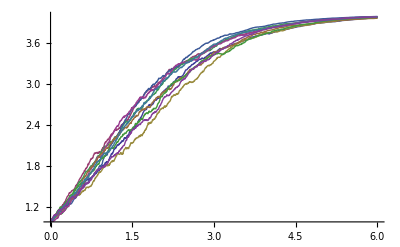

```mathematica
Show[ListLinePlot[stochsol]]
```